```mathematica
datapointM=Import["D:\\project\\formula derivation\\spectra.png.dat","Data"]
```

{{0.999231,3.14516},{0.999231,1.23992},{0.999231,4.6875},{2.99769,-0.9375},{2.99769,-3.20565},{2.99769,1.23992},{4.99616,-5.92742},{4.99616,-10.1008},{5.03459,-2.11694},{6.99462,8.04435},{6.99462,0.0604839},{6.99462,15.8468},{8.99308,11.129},{9.03151,0.423387},{8.99308,21.4718},{10.9915,24.0121},{11.03,11.4012},{11.03,36.623},{13.0284,25.0101},{13.0284,13.9415},{12.99,36.0786},{15.0269,21.1089},{15.0269,11.0383},{15.0269,30.8165},{16.9869,17.1169},{17.0254,8.04435},{17.0254,25.9173},{18.9854,4.95968},{19.0238,-3.02419},{19.0238,13.0343},{20.9839,9.9496},{21.0223,2.51008},{21.0223,17.3891},{22.9823,6.04839},{23.0208,-0.9375},{23.0208,12.8528},{25.0192,-0.0302419},{25.0192,-6.47177},{25.0192,6.41129},{27.0177,5.0504},{27.0177,-2.93347},{27.0177,12.8528},{29.0161,9.04234},{29.0161,2.41935},{29.0161,15.4839},{31.0146,5.95766},{31.053,0.15121},{31.0146,11.7641},{33.0131,-5.11089},{33.0131,-10.373},{33.0131,0.332661},{35.0115,4.95968},{35.0115,-1.3004},{35.0115,11.3105},{36.9716,15.0302},{37.01,8.86089},{37.01,21.1089},{39.0085,-0.9375},{39.0085,-7.74194},{39.0085,5.68548},{41.0069,-0.9375},{41.0069,-7.28831},{41.0069,5.32258},{43.0054,-4.02218},{43.0054,-9.46573},{43.0054,1.42137},{45.0038,-4.92944},{45.0038,-11.0988},{45.0038,1.05847},{47.0023,8.13508},{47.0023,2.05645},{47.0023,13.9415},{49.0008,-7.01613},{49.0008,-13.4577},{49.0008,-0.665323}}

```mathematica
dataDow=Table[{2 i-1,#1[[3i-3+#2,2]]},{i,1,Length[#1]/3}]&[datapointM,2];
dataCen=Table[{2 i-1,#1[[3i-3+#2,2]]},{i,1,Length[#1]/3}]&[datapointM,1];
dataUp=Table[{2 i-1,#1[[3i-3+#2,2]]},{i,1,Length[#1]/3}]&[datapointM,3];
daraErr=Table[{#2[[i,2]]-#1[[i,2]],#3[[i,2]]-#1[[i,2]]},{i,1,Length[#1]}]&[dataCen,dataDow,dataUp];
```

{1.72379,2.22278,3.99194,7.89315,10.5242,12.6109,11.0685,9.88911,8.93649,8.02923,7.43952,6.89516,6.44153,7.89315,6.53226,5.80645,5.35282,6.30544,6.12399,6.71371,6.30544,5.44355,6.07863,5.94254,6.39617}

{3.14516,-0.9375,-5.92742,8.04435,11.129,24.0121,25.0101,21.1089,17.1169,4.95968,9.9496,6.04839,-0.0302419,5.0504,9.04234,5.95766,-5.11089,4.95968,15.0302,-0.9375,-0.9375,-4.02218,-4.92944,8.13508,-7.01613}

{{1,3.11.7},{3,-0.92.2},{5,-6.4.},{7,8.8.},{9,11.11.},{11,24.13.},{13,25.11.},{15,21.10.},{17,17.9.},{19,5.8.},{21,10.7.},{23,6.7.},{25,0.6.},{27,5.8.},{29,9.7.},{31,6.6.},{33,-5.5.},{35,5.6.},{37,15.6.},{39,0.7.},{41,0.6.},{43,-4.5.},{45,-5.6.},{47,8.6.},{49,-7.6.}}

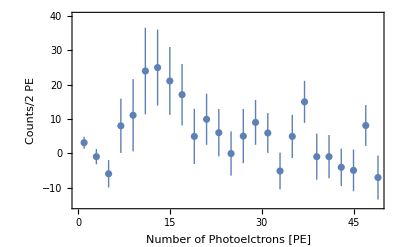

```mathematica
dataErr=Table[(-(#2[[i,2]]-#1[[i,2]])+#3[[i,2]]-#1[[i,2]])/2,{i,1,Length[#1]}]&[dataCen,dataDow,dataUp]
dataCen=Table[#1[[3i-3+#2,2]],{i,1,Length[#1]/3}]&[datapointM,1]
coherentdataM=Table[{dataCen[[i]],ErrorBar[dataErr[[i]]]},{i,1,Length[dataCen]}];
coherentdataM=Table[{2 i-1,Around[dataCen[[i]],dataErr[[i]]]},{i,1,Length[dataCen]}]
pic1=ListPlot[coherentdataM,Frame->True,AxesOrigin->{0,-15},PlotRange->{-15,40},FrameLabel->{"Number of Photoelctrons [PE]","Counts/2 PE"}]
```